KerrGeodesics > KerrGeodesics

# Kerr Geodesics

The KerrGeodesics package provides functions for computing quantities related to bound timelike geodesic orbits in Kerr spacetime. Before using the functions, first load the package

```mathematica
<<KerrGeodesics`
```

### Constants of motion and orbital frequencies

```mathematica
KerrGeoELQ[0.9`20,10,0.5`20,π/3]
```

{0.964707445161354724,1.8188419221975734,9.9666815875696189}

```mathematica
KerrGeoFreqs[0.9`20,10,0.5`20,π/3]
```

{0.0158269739397,0.0213671693254,0.022541486256,170.471989197}

### Photon sphere, IBSO and ISSO

Radius of the photon sphere for a=M

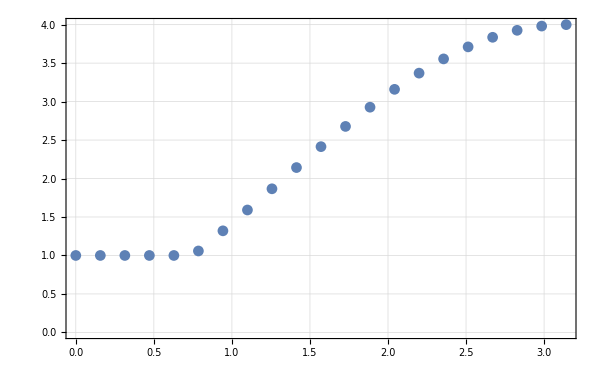

```mathematica
Table[{θ,KerrGeoPhotonSphereRadius[1,θ]},{θ,0,π,π/20.}];
ListPlot[%,PlotTheme->"Detailed",ImageSize->600]
```

```mathematica
PlotSpherical[a_]:=Block[{rph,rmb,rms,n=30},
rph=Table[{KerrGeoPhotonSphereRadius[a,θ],180 θ/π},{θ,0,π,π/n}];
rmb=Table[{KerrGeoIBSO[a,θ],180 θ/π},{θ,0,π,π/n}];
rms=Table[{KerrGeoISSO[a,θ],180 θ/π},{θ,0,π,π/n}];
Show[
Plot[180,{r,rmb[[-1,1]],rms[[-1,1]]},PlotStyle->None,Filling->Axis,FillingStyle->LightRed,PlotTheme->"Detailed",Frame->True,ImageSize->800,Axes->False,BaseStyle->20,FrameLabel->{"r/M","θ_inc"}],
Plot[180,{r,rms[[-1,1]],10},PlotStyle->None,Filling->Axis,FillingStyle->LightBlue],
ListPlot[{rph,rmb,rms,7},Filling->{2->{Axis,LightRed},3->{Axis,LightBlue}},Joined->True,PlotStyle->{Green,Red,Blue}],
PlotRange->All
]
]
```

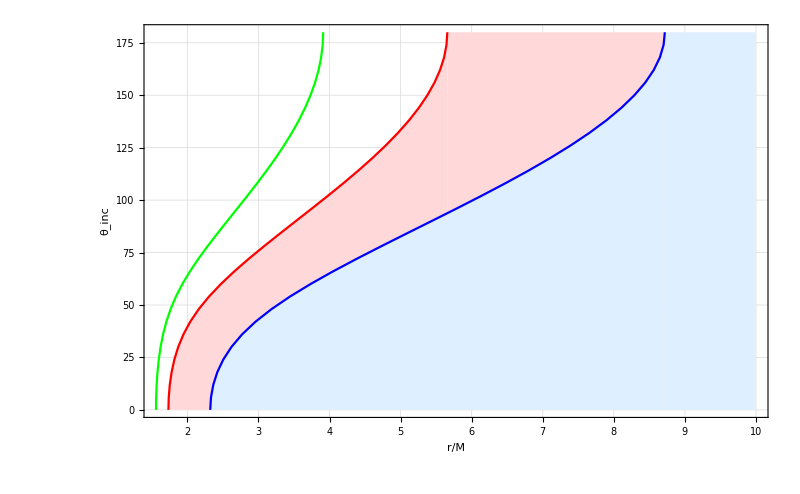

```mathematica
PlotSpherical[0.9]
```